Theorem  (Runge-Kutta Method of order 4)  Assume that  f(t,y)  is continuous and satisfies a Lipschits condition in the variable  y,  and consider the  I. V. P. (initial value problem) 

		y' = f(t,y) with y(a)=t_0=α,  over the interval  a≤t≤b. 
		
The Runge-Kutta method uses the formulas t_(k+1) = t_k+h,  and  

		y_(j+1) = y_j+1/6(k_1+2 k_2+2 k_3+k_4)     for  k=0,1,2,... ,m-1  
where
		k_1=h f(t_j,y_j)
k_2=h f(t_j+h/2,y_j+k_1/2)
k_3=h f(t_j+h/2,y_j+k_2/2)
k_4=h f(t_j+h,y_j+k_3)   

as an approximate solution to the differential equation using the discrete set of points  {(t_k,y_k)}_(k=0)^m.

Theorem  (Precision  of the Runge-Kutta Method of Order 4)  Assume that   y=y(t)  is the solution to the I.V.P.  y' = f(t,y)  with  y(t_0)=y_0.  If  y(t)∈C^2[t_0,b]  and  {(t_k,y_k)}_(k=0)^m  is the sequence of approximations generated by the Runge-Kutta method of order 4, then at each step, the local truncation error is of the order  O(h^5),  and the overall global truncation error  e_k  is of the order

		|e_k| = |y(t_k) - y_k| = O(h^4),  for  k=1,2,... ,m.  


The error at the right end of the interval is called the final global error  

		E(y(b),h) = |y(b) - y_m| = O(h^4).

Algorithm (Runge-Kutta  Method). To compute a numerical approximation for the solution of the initial value problem  y' = f(t,y)  with  y(t_0)=y_0=α  over  [t_0,b]=[a,b]  at a discrete set of points using the formula  

	y_(j+1) = y_j+1/6(k_1+2 k_2+2 k_3+k_4),  for  k=0,1,2,... ,m-1  
where 
	k_1=h f(t_j,y_j), 
	k_2=h f(t_j+h/2,y_j+k_1/2), 
	k_3=h f(t_j+h/2,y_j+k_2/2), and 
	k_4=h f(t_j+h,y_j+k_3).

Mathematica Subroutine (Runge-Kutta Method of Order 4).

```mathematica
Runge[a0_,b0_,α_,m0_]:=
Module[{a=a0,b=b0,j,m=m0},
h=(b-a)/m; 
Y = T = Table[0,{m+1}]; 
T_⟦1⟧ = a; 
Y_⟦1⟧ = α; 
For[ j=1, j≤m, j++,
Subscript[k, 1] = h  f[T_⟦j⟧,Y_⟦j⟧]; 
Subscript[k, 2] = h  f[T_⟦j⟧+h/2,Y_⟦j⟧+Subscript[k, 1]/2]; 
Subscript[k, 3] = h  f[T_⟦j⟧+h/2,Y_⟦j⟧+Subscript[k, 2]/2]; 
Subscript[k, 4] = h  f[T_⟦j⟧+h,Y_⟦j⟧+Subscript[k, 3]]; 
Y_⟦j+1⟧ = Y_⟦j⟧+1/6(Subscript[k, 1]+2 Subscript[k, 2]+2 Subscript[k, 3]+Subscript[k, 4]); 
T_⟦j+1⟧ = a+h  j; ]; 
Return[Transpose[{T,Y}]] ]
```

Solution 1.

Compute the Runge-Kutta solution based on 25 subintervals and plot the results.

```mathematica
f[t_,y_] = 1 - t  y; 
Print["Find numerical solutions to the D.E."]; 
Print["y' = ",f[t,y] ];
```

Find numerical solutions to the D.E.

y' = 1-t y

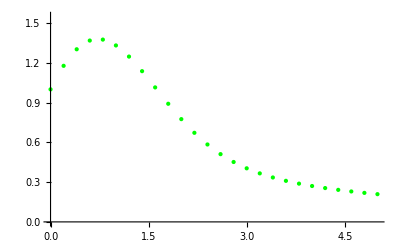

The Runge-Kutta solution for  y' = 1-t y

Using  n = 26  points.

{{0.,1.},{0.2,1.17755},{0.4,1.30245},{0.6,1.36819},{0.8,1.37546},{1.,1.3313},{1.2,1.24732},{1.4,1.13727},{1.6,1.01473},{1.8,0.89124},{2.,0.77533},{2.2,0.672211},{2.4,0.584154},{2.6,0.511195},{2.8,0.451948},{3.,0.404325},{3.2,0.366085},{3.4,0.335157},{3.6,0.309811},{3.8,0.288687},{4.,0.270764},{4.2,0.255297},{4.4,0.241752},{4.6,0.229741},{4.8,0.218982},{5.,0.209267}}

The final value is  y(5) = y_26 = 0.209267

```mathematica
n=25; 
pts1 =Runge[0.0,5.0,1.0,n]; 
Y1 = Y; 
graph1 = ListPlot[pts1,PlotStyle-> Green,PlotRange->{{0,5},{0,1.55}}]
Print["The Runge-Kutta solution for  y' = ",f[t,y] ]; 
Print["Using  n = ",n+1,"  points."];
Print[pts1]; 
Print[""];
Print["The final value is  y(5) = ",Subscript[y, n+1]," = ",Y_⟦n+1⟧];
```

Example 2.  Solve the I.V.P.  y'= t^2 +y^2  with   y(0) = 1  over  0≤t≤1.

Example 3.  Solve the I.V.P.  y'= 1- t y^(1/3)  with   y(0) = 1  over  0≤t≤5.

```mathematica
f[t_,y_] = 1- t y^(1/3); 
Print["Find numerical solutions to the D.E."]; 
Print["y' = ",f[t,y] ];
```

Find numerical solutions to the D.E.

y' = 1-t y^(1/3)

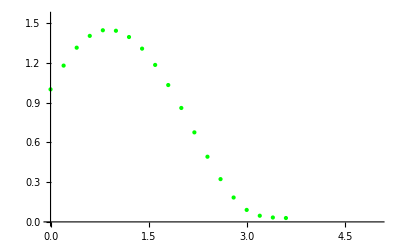

The Runge-Kutta solution for  y' = 1-t y^(1/3)

Using  n = 26  points.

{{0.,1.},{0.2,1.17921},{0.4,1.31445},{0.6,1.4035},{0.8,1.44579},{1.,1.44217},{1.2,1.39482},{1.4,1.30726},{1.6,1.18437},{1.8,1.03249},{2.,0.859591},{2.2,0.675422},{2.4,0.491797},{2.6,0.322719},{2.8,0.183981},{3.,0.0904276},{3.2,0.0465658},{3.4,0.0332384},{3.6,0.029252},{3.8,0.0383911-0.0186821 ⅈ},{4.,0.007051-0.0497946 ⅈ},{4.2,-0.080578-0.0869082 ⅈ},{4.4,-0.245496-0.120009 ⅈ},{4.6,-0.488049-0.151853 ⅈ},{4.8,-0.809117-0.183513 ⅈ},{5.,-1.21088-0.215334 ⅈ}}

The final value is  y(5) = y_26 = -1.21088-0.215334 ⅈ

```mathematica
n=25; 
pts1 =Runge[0.0,5.0,1.0,n]; 
Y1 = Y; 
graph1 = ListPlot[pts1,PlotStyle-> Green,PlotRange->{{0,5},{0,1.55}}]
Print["The Runge-Kutta solution for  y' = ",f[t,y] ]; 
Print["Using  n = ",n+1,"  points."];
Print[pts1]; 
Print[""];
Print["The final value is  y(5) = ",Subscript[y, n+1]," = ",Y_⟦n+1⟧];
```

```mathematica
NDSolve[{y'[t]= 1- t y^(1/3),y[0]==1},y,{t,0,5}]
```

NDSolve::deqn: Equation or list of equations expected instead of 1 - t\ y^1/3 in the first argument {1 - t\ y^1/3, y[0] == 1}.

NDSolve[{1-t y^(1/3),y[0]==1},y,{t,0,5}]

## Ejemplo

```mathematica
Runge[0.0,5.0,1.0,25]
```

{{0.,1.},{0.2,1.17755},{0.4,1.30245},{0.6,1.36819},{0.8,1.37546},{1.,1.3313},{1.2,1.24732},{1.4,1.13727},{1.6,1.01473},{1.8,0.89124},{2.,0.77533},{2.2,0.672211},{2.4,0.584154},{2.6,0.511195},{2.8,0.451948},{3.,0.404325},{3.2,0.366085},{3.4,0.335157},{3.6,0.309811},{3.8,0.288687},{4.,0.270764},{4.2,0.255297},{4.4,0.241752},{4.6,0.229741},{4.8,0.218982},{5.,0.209267}}

```mathematica
Euler[0.0,5.0,1.0,25]
```

{{0.,1.},{0.2,1.2},{0.4,1.352},{0.6,1.44384},{0.8,1.47058},{1.,1.43529},{1.2,1.34823},{1.4,1.22465},{1.6,1.08175},{1.8,0.935591},{2.,0.798778},{2.2,0.679267},{2.4,0.580389},{2.6,0.501803},{2.8,0.440865},{3.,0.393981},{3.2,0.357592},{3.4,0.328733},{3.6,0.305195},{3.8,0.285454},{4.,0.268509},{4.2,0.253702},{4.4,0.240592},{4.6,0.228871},{4.8,0.21831},{5.,0.208732}}

```mathematica
EulerM[0.0,5.0,1.0,25]
```

{{0.,1.},{0.2,1.178},{0.4,1.30273},{0.6,1.36767},{0.8,1.37369},{1.,1.3282},{1.2,1.24322},{1.4,1.13277},{1.6,1.01052},{1.8,0.887912},{2.,0.773239},{2.2,0.671431},{2.4,0.584521},{2.6,0.512403},{2.8,0.453647},{3.,0.406204},{3.2,0.367911},{3.4,0.336793},{3.6,0.311195},{3.8,0.289813},{4.,0.271659},{4.2,0.256003},{4.4,0.242309},{4.6,0.230185},{4.8,0.219343},{5.,0.209566}}

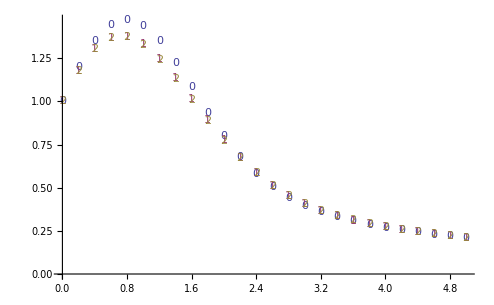

```mathematica
ListPlot[{Euler[0.0,5.0,1.0,25],Runge[0.0,5.0,1.0,25],EulerM[0.0,5.0,1.0,25]},PlotMarkers->{"0","1","2"}]
```

```mathematica
fa[t_]:=1/2 ⅇ^(-t^2/2) (2+√(2 π) Erfi[t/(√2)])
```

```mathematica
Table[Euler[0.0,5.0,1.0,25][[i,1]],{i,1,Length[Euler[0.0,5.0,1.0,25]]}]
```

{0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.}

```mathematica
TableForm[Table[{Euler[0.0,5.0,1.0,25][[i,1]],fa[Euler[0.0,5.0,1.0,25][[i,1]]],Euler[0.0,5.0,1.0,25][[i,2]],EulerM[0.0,5.0,1.0,25][[i,2]],Runge[0.0,5.0,1.0,25][[i,2]],Abs[(fa[Euler[0.0,5.0,1.0,25][[i,1]]]-Euler[0.0,5.0,1.0,25][[i,2]])/fa[Euler[0.0,5.0,1.0,25][[i,1]]]*100],Abs[(fa[Euler[0.0,5.0,1.0,25][[i,1]]]-EulerM[0.0,5.0,1.0,25][[i,2]])/fa[Euler[0.0,5.0,1.0,25][[i,1]]]*100],Abs[(fa[Euler[0.0,5.0,1.0,25][[i,1]]]-Runge[0.0,5.0,1.0,25][[i,2]])/fa[Euler[0.0,5.0,1.0,25][[i,1]]]*100]},{i,1,Length[Euler[0.0,5.0,1.0,25]]}],TableHeadings->{None,{"Tiempo","Función(t)","Euler","Euler Mejorado","Runge-Kutta","Error Euler","Error Euler Mejo.","Error Runge-Kutta"}}]
```

Tiempo | Función(t) | Euler | Euler Mejorado | Runge-Kutta | Error Euler | Error Euler Mejo. | Error Runge-Kutta
0. | 1. | 1. | 1. | 1. | 0. | 0. | 0.
0.2 | 1.17755 | 1.2 | 1.178 | 1.17755 | 1.90622 | 0.0379415 | 0.000114809
0.4 | 1.30245 | 1.352 | 1.30273 | 1.30245 | 3.80434 | 0.0217475 | 0.000222243
0.6 | 1.3682 | 1.44384 | 1.36767 | 1.36819 | 5.52859 | 0.0385 | 0.00035438
0.8 | 1.37546 | 1.47058 | 1.37369 | 1.37546 | 6.91509 | 0.129333 | 0.000530481
1. | 1.33131 | 1.43529 | 1.3282 | 1.3313 | 7.81016 | 0.23329 | 0.000746361
1.2 | 1.24733 | 1.34823 | 1.24322 | 1.24732 | 8.08903 | 0.329756 | 0.000957828
1.4 | 1.13729 | 1.22465 | 1.13277 | 1.13727 | 7.68213 | 0.397076 | 0.00106673
1.6 | 1.01474 | 1.08175 | 1.01052 | 1.01473 | 6.60414 | 0.415938 | 0.000920179
1.8 | 0.891243 | 0.935591 | 0.887912 | 0.89124 | 4.97592 | 0.373719 | 0.000334434
2. | 0.775323 | 0.798778 | 0.773239 | 0.77533 | 3.02515 | 0.268847 | 0.000850457
2.2 | 0.672193 | 0.679267 | 0.671431 | 0.672211 | 1.05234 | 0.113427 | 0.00269395
2.4 | 0.584125 | 0.580389 | 0.584521 | 0.584154 | 0.639436 | 0.0679309 | 0.00508737
2.6 | 0.511156 | 0.501803 | 0.512403 | 0.511195 | 1.82983 | 0.244048 | 0.00774003
2.8 | 0.451901 | 0.440865 | 0.453647 | 0.451948 | 2.44213 | 0.386302 | 0.0102473
3. | 0.404276 | 0.393981 | 0.406204 | 0.404325 | 2.54657 | 0.476921 | 0.0122209
3.2 | 0.366035 | 0.357592 | 0.367911 | 0.366085 | 2.30665 | 0.512517 | 0.0134155
3.4 | 0.335111 | 0.328733 | 0.336793 | 0.335157 | 1.9032 | 0.501848 | 0.0137892
3.6 | 0.309769 | 0.305195 | 0.311195 | 0.309811 | 1.47682 | 0.46007 | 0.013477
3.8 | 0.28865 | 0.285454 | 0.289813 | 0.288687 | 1.10703 | 0.40286 | 0.0127116
4. | 0.270732 | 0.268509 | 0.271659 | 0.270764 | 0.820989 | 0.342615 | 0.0117362
4.2 | 0.25527 | 0.253702 | 0.256003 | 0.255297 | 0.614284 | 0.287162 | 0.0107457
4.4 | 0.241728 | 0.240592 | 0.242309 | 0.241752 | 0.469841 | 0.240206 | 0.00986328
4.6 | 0.22972 | 0.228871 | 0.230185 | 0.229741 | 0.36946 | 0.202553 | 0.00914473
4.8 | 0.218963 | 0.21831 | 0.219343 | 0.218982 | 0.298595 | 0.173383 | 0.00859777
5. | 0.209249 | 0.208732 | 0.209566 | 0.209267 | 0.24712 | 0.151204 | 0.00820298

```mathematica
EEuler=Table[{Euler[0.0,5.0,1.0,25][[i,1]],Abs[(fa[Euler[0.0,5.0,1.0,25][[i,1]]]-Euler[0.0,5.0,1.0,25][[i,2]])/fa[Euler[0.0,5.0,1.0,25][[i,1]]]*100]},{i,1,Length[Euler[0.0,5.0,1.0,25]]}];
```

```mathematica
EEulerM=Table[{Euler[0.0,5.0,1.0,25][[i,1]],Abs[(fa[Euler[0.0,5.0,1.0,25][[i,1]]]-EulerM[0.0,5.0,1.0,25][[i,2]])/fa[Euler[0.0,5.0,1.0,25][[i,1]]]*100]},{i,1,Length[Euler[0.0,5.0,1.0,25]]}];
```

```mathematica
ERunge=Table[{Euler[0.0,5.0,1.0,25][[i,1]],Abs[(fa[Euler[0.0,5.0,1.0,25][[i,1]]]-Runge[0.0,5.0,1.0,25][[i,2]])/fa[Euler[0.0,5.0,1.0,25][[i,1]]]*100]},{i,1,Length[Euler[0.0,5.0,1.0,25]]}];
```

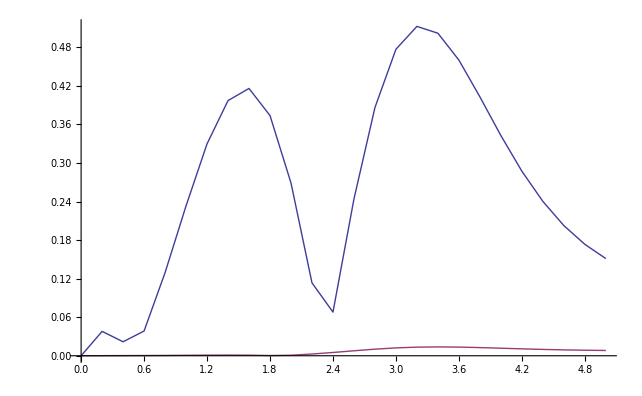

```mathematica
ListLinePlot[{EEulerM,ERunge}]
```

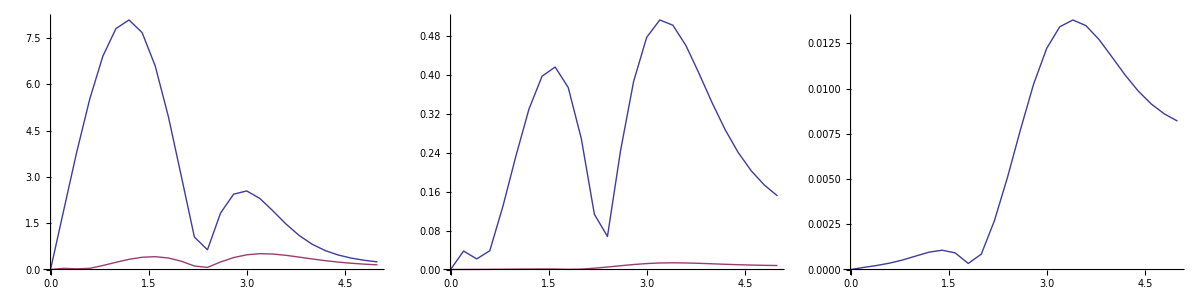

```mathematica
Grid[{{ListLinePlot[{EEuler,EEulerM}],ListLinePlot[{EEulerM,ERunge}],ListLinePlot[{ERunge}],ListLinePlot[{Euler}]}}]
```